# Exporter Test

### Generate Graph and Association from Twine Project

#### Importer

```mathematica
Clear[generateEdges]
generateEdges[parentName_, links_]:= Thread[DirectedEdge[parentName, links]]
Clear[extractLinks]
extractLinks[passageContent_]:=DeleteCases[StringCases[passageContent,("[["~~ShortestMatch[p___]~~"]]"):> p], {}]
```

```mathematica
Clear[twineImport]
twineImport[absoluteFilePath_String]:=Module[{fileAsString,xmlObject, rootNode,rootNodeName, passages,passageContentThread,passageAssociation,assocForm,edges,alledges, g, v},
fileAsString = Import[absoluteFilePath, "String"];
xmlObject = parseXML[fileAsString];
rootNode = Cases[xmlObject, XMLElement["tw-storydata", {Rule["name", name_],___}, _]];
rootNodeName =Cases[xmlObject, XMLElement["tw-storydata", {Rule["name", name_],___}, _]:> name]/.{storytitle_}->storytitle;
passages = Cases[rootNode, XMLElement["tw-passagedata", {___,Rule["name", name_],___}, content_]:> {name,content}, {0, Infinity}];
passageContentThread= AssociationThread[Transpose[passages]⟦1⟧ -> StringReplace[Transpose[passages]⟦2⟧, ("[["~~ShortestMatch[p___]~~"]]"):> p]];
passageAssociation =AssociateTo[passageContentThread, rootNodeName -> "Start Here"];
links= DeleteCases[extractLinks[#⟦2⟧]&/@passages, {}];
edges =generatedEdges[#⟦1⟧, extractLinks[#⟦2⟧]]&/@passages;
alledges= Flatten[{{rootNodeName -> First[passages]⟦1⟧},DeleteCases[edges, {}]}];
g =Graph[alledges];
v =Table[Tooltip[VertexList[g]⟦i⟧, passageAssociation[VertexList[g]⟦i⟧]], {i, 1, Length[VertexList[g]]}];
completeGraph = Graph[v, alledges, VertexLabels->"Name",GraphLayout ->{"LayeredDigraphEmbedding", "RootVertex"->rootNodeName}
];
assocForm = Block[{passageContentWithLinks,completeAssociation},
(*Create Assocation between passage and content for tooltips and remove the link syntax*)
passageContentWithLinks= AssociationThread[Transpose[passages]⟦1⟧ -> Transpose[passages]⟦2⟧];
(*Root Node Association*)
completeAssociation = <|rootNodeName -> passageContentWithLinks|>];
{completeGraph, assocForm}
]
twineImport::usage = "twineImport[path/to/file.html] gives a graph and an association of a Twine 2 project";
```

#### Exporter : Rewrite

```mathematica
Clear[twineExport]
twineExport[associationForm_Association | storyGraph_Graph, exportPathToFile_]:=Module[{storyAssoc = associationForm , sTemplateHeader,assocLength,passageAssoc,passages, stringOfStory},
sTemplateHeader = StringTemplate["
<tw-storydata name=\"`storyTitle`\" startnode=\"1\" creator=\"Twine\" creator-version=\"2.2.1\" zoom=\"1\" format=\"Harlowe\" format-version=\"2.1.0\" options=\"\" hidden>

  <style role=\"stylesheet\" id=\"twine-user-stylesheet\" type=\"text/twine-css\">
  </style>
  <script role=\"script\" id=\"twine-user-script\" type=\"text/twine-javascript\">
  </script>
"
][<|"storyTitle" -> First[Keys[storyAssoc]]|>];
passageAssoc = First[Values[storyAssoc]];
assocLength = Length[passageAssoc];
passages=Table[
StringTemplate["<tw-passagedata pid=\"`pid`\" 
name=\"`passagename`\" 
tags=\"\"
position=\"320,377\"
size=\"100,100\"
>`content`</tw-passagedata>"][<|"pid"-> index,"passagename" -> Keys[passageAssoc]⟦index⟧, "content" -> Values[passageAssoc]⟦index⟧|>], {index, 1,assocLength,1}];
stringOfStory= StringJoin[{sTemplateHeader, passages, "</tw-storydata>"}];
Export[exportPathToFile <>".html",stringOfStory , "HTMLFragment"]
]
twineExport::usage = "twineExport[<| key1 → val1 ... |>, path/to/file] Exports WL Twine Representation to the specified path";
```

```mathematica
twineAssoc
```

<|TwineBridge_Test→<|First Passage→This is my first passage. Where can I go from here? How about [[Left]] , or [[Right]]?,Left→From here, there are still other places to go. We can go [[Up]] or [[Down]],Right→From here, there are still other places to go. We can go [[Up]] or [[Down]],Up→Now that we are up why don&#39;t we [[get going]]?,Down→Now that we are down, why don&#39;t we get [[Up]]?,get going→Now that we are going, how about we [[do something]],do something→ Hi, I&#39;m doing something, why don&#39;t [[you do something]]?,you do something→ Go, Get out of here! |>|>

```mathematica
twineAssoc["TwineBridge_Test"]["First Passage"]
```

This is my first passage. Where can I go from here? How about [[Left]] , or [[Right]]?

```mathematica
Values[twineAssoc]//First
```

<|First Passage→This is my first passage. Where can I go from here? How about [[Left]] , or [[Right]]?,Left→From here, there are still other places to go. We can go [[Up]] or [[Down]],Right→From here, there are still other places to go. We can go [[Up]] or [[Down]],Up→Now that we are up why don&#39;t we [[get going]]?,Down→Now that we are down, why don&#39;t we get [[Up]]?,get going→Now that we are going, how about we [[do something]],do something→ Hi, I&#39;m doing something, why don&#39;t [[you do something]]?,you do something→ Go, Get out of here! |>

```mathematica
twineExport[twineAssoc, "~/Desktop/newForm-export-01"]
```

~/Desktop/newForm-export-01.html

#### WL Native

```mathematica
Clear[twineSummary]
twineSummary[userAssoc_, outputForm_:"Summary"]:=Module[{firstEdge, passageEdges,psgContent},
(*First Edge*)
firstEdge = {First[Keys[userAssoc]]-> Flatten[Keys[Values[userAssoc]]]⟦1⟧};
(*Passage Edges*)
passageEdges = Flatten@DeleteCases[Table[generateEdges[Flatten[Keys[Values[userAssoc]]]⟦index⟧, extractLinks[Flatten[Values[Values[userAssoc]]]⟦index⟧]], {index, 1, Length[Values[userAssoc]/.{assc_}:> assc],1}], {}];
(*Passage Content*)
psgContent =Table[generateEdges[Flatten[Keys[Values[userAssoc]]]⟦index⟧,Flatten[Values[Values[userAssoc]]]⟦index⟧], {index, 1, Length[Values[userAssoc]/.{assc_}:> assc],1}];
(*
 Summary ⇒ {Edges, Simple Graph} 
 Export  ⇒ Exports Story to TwineStories folder in current directory
*)
Switch[outputForm,
"Summary", GraphicsRow[{Framed[Column[{First[Keys[userAssoc]],Column[Framed/@Normal[psgContent]⟦All,2⟧ ]}]], Graph[Flatten[firstEdge~Join~passageEdges], VertexShapeFunction -> "Name"]}],
"Export",
If[DirectoryQ[FileNameJoin[{NotebookDirectory[], "TwineStories"}]],
Block[{twineFolder},
twineFolder = FileNameJoin[{NotebookDirectory[], "TwineStories"}];
exportTwineProject[userAssoc, twineFolder <> "/"<> ToString[First[Keys[userAssoc]]]]
],
Block[{twineFolder},
twineFolder = FileNameJoin[{NotebookDirectory[], "TwineStories"}];
CreateDirectory[twineFolder];
exportTwineProject[userAssoc, twineFolder <> "/"<> ToString[First[Keys[userAssoc]]]]]
];
]
]
twineSummary::usage = "twineSummary[<| key1 → val1 ... |>, \"Export\"] Exports WL Twine Representation to the TwineStories folder in the Current Notebook Directory";
twineSummary::usage = "twineSummary[<| key1 → val1 ... |>] Displays the Twine Passages and the Graph";
```

### Import Twine Story

```mathematica
Clear[twineGraph, twineAssoc]
```

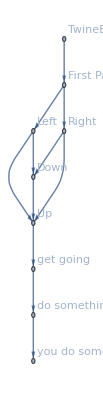
{-Graphics-,<|TwineBridge_Test→<|First Passage→This is my first passage. Where can I go from here? How about [[Left]] , or [[Right]]?,Left→From here, there are still other places to go. We can go [[Up]] or [[Down]],Right→From here, there are still other places to go. We can go [[Up]] or [[Down]],Up→Now that we are up why don&#39;t we [[get going]]?,Down→Now that we are down, why don&#39;t we get [[Up]]?,get going→Now that we are going, how about we [[do something]],do something→ Hi, I&#39;m doing something, why don&#39;t [[you do something]]?,you do something→ Go, Get out of here! |>|>}

```mathematica
{twineGraph, twineAssoc} =twineImport["~/Documents/Twine/Stories/TwineBridge_Test.html"]
```

### Display or Export Twine Story from Association

### Different Forms

```mathematica
testingAssoc =<|"Other Story" -><|"Two" -> "Go to passage [[Three]]", "Three" ->  "Here we are at Passage Three"|>|>;
```

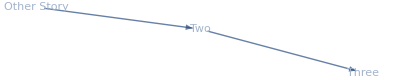

```mathematica
twineSummary[testingAssoc]
```

```mathematica
twineSummary[testingAssoc, "Export"]
```

```mathematica
twineAssoc
```

<|TwineBridge_Test→<|First Passage→This is my first passage. Where can I go from here? How about [[Left]] , or [[Right]]?,Left→From here, there are still other places to go. We can go [[Up]] or [[Down]],Right→From here, there are still other places to go. We can go [[Up]] or [[Down]],Up→Now that we are up why don&#39;t we [[get going]]?,Down→Now that we are down, why don&#39;t we get [[Up]]?,get going→Now that we are going, how about we [[do something]],do something→ Hi, I&#39;m doing something, why don&#39;t [[you do something]]?,you do something→ Go, Get out of here! |>|>

```mathematica
twineAssocNewForm = <|"TwineBridge_Test"-><|"First Passage"->"This is my first passage. Where can I go from here? How about [[Left]] , or [[Right]]?","Left"->"From here, there are still other places to go. We can go [[Up]] or [[Down]]","Right"->"From here, there are still other places to go. We can go [[Up]] or [[Down]]","Up"->"Now that we are up why don&#39;t we [[get going]]?","Down"->"Now that we are down, why don&#39;t we get [[Up]]?","get going"->"Now that we are going, how about we [[do something]]","do something"->" Hi, I&#39;m doing something, why don&#39;t [[you do something]]?","you do something"->" Go, Get out of here! "|>|>;
```

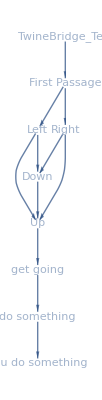

```mathematica
twineSummary[twineAssocNewForm]
```

The left graphic will turn into the GUI. What might be interesting as well is to highlight the graph on the right as one moves through the story on the left.

```mathematica
twineSummary[twineAssoc, "Export"]
```

### Position of Passages

I can use the vertex positions from the graph for passage positions

```mathematica
testFN[representationForm_Association | representationForm_Graph]:=Module[{rf = representationForm},
Switch[AssociationQ[rf],
True, Echo[rf, "Associaton"] ,
False, Echo[rf, "Graph"]
]

]
```

```mathematica
testFN[<|"Test" -> "Thing"|>]
```

Associaton <|Test→Thing|>

<|Test→Thing|>

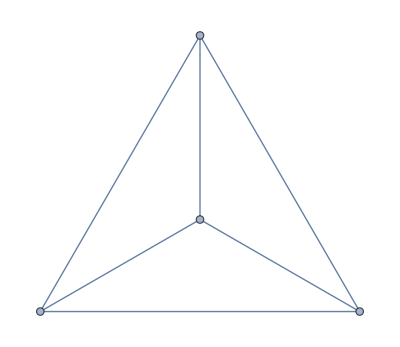
Graph -Graphics-

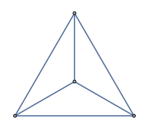

```mathematica
testFN[CompleteGraph[4]]
```